Answer for 6(a)

```mathematica
DSolve[{y'[x]==  y[x]^2 Sin[x]^2},y[x],x]
```

{{y[x]→4/(-2 x-4 C[1]+Sin[2 x])}}

```mathematica
sol = y[x] /. %1/. C[1] -> a
```

{4/(-4 a-2 x+Sin[2 x])}

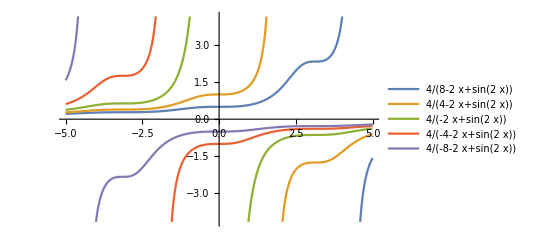

```mathematica
Plot[Evaluate[Table[sol,{a,-2,2}]],{x,-5,5},PlotLegends -> "Expressions"]
```

Answer for 6(b)

```mathematica
DSolve[{v'[t]- (1/5)v [t]Tan[t/5] == 20 ,v[0]== 1} ,v[t],t]
```

{{v[t]→Sec[t/5]+100 Tan[t/5]}}

```mathematica
v[t] /. %4 /. t -> 3//N
```

{69.6253}

Answer for 6(c)

```mathematica
NDSolve[{x'[t] == y[t]^(2) + x[t]y[t] , 2x[t]^(2) + y[t]^(2) == 1 , x[0] == 0 }, {x[t],y[t]},{t,0,5}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

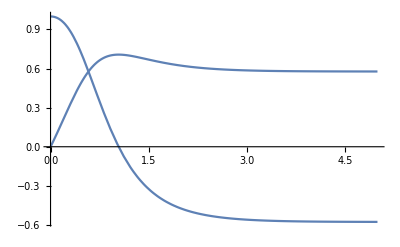

```mathematica
Plot[{y[t],x[t]} /. %6 , {t,0,5}]
```